```mathematica
Clear["Global`*"]
```

```mathematica
dataDir="~/Dropbox/"(*"../../matlab/ruslan/";*)
```

~/Dropbox/

```mathematica
dataDir<>"ks22tw1manif.mat"
```

~/Dropbox/ks22tw1manif.mat

```mathematica
d=62; (* state space dimension (real numbers, not counting zero mode*)
```

```mathematica
dF=31; (* n/2-1, where n the number of Fourier modes counting zero mode *)
```

Import set of trajectories (here for unstable manifold of TW1). (Nic x d)-rows Nsteps-columns, where Nic the number of initial conditions, d the state-space dimension, Nsteps the number of time steps.

```mathematica
tw1manif=Import[dataDir<>"ks22tw1manif.mat"];
```

```mathematica
tw1manif[[1]]//Dimensions
```

{1054,901}

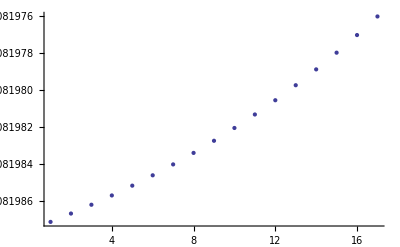

```mathematica
ListPlot[tw1manif[[1,1;;-1;;d,10]] ,PlotRange->All]
```

```mathematica
tw1manif[[1]]//Dimensions
```

{1054,901}

```mathematica
Length[Table[i,{i,0,1,0.06}]]
```

17

```mathematica
1054/17
```

62

```mathematica
901/17
```

53

```mathematica
rpo1=Import[dataDir<>"ks22rpo16p31s2.86.mat"] ;(*,"LabeledData"]*)
```

```mathematica
rpo2=Import[dataDir<>"ks22rpo55p6s5p25.mat"] ;
```

```mathematica
rpo3=Import[dataDir<>"ks22rpo77p85s10p8.mat"] ;
```

```mathematica
rpo1[[1]]//Dimensions
```

{62,165}

```mathematica
rpo3[[1]]//Dimensions
```

{62,647}

```mathematica
rotList[th_,dF_]:=Table[Exp[I k th],{k,1,dF}]
```

```mathematica
rot[th_,dF_]:=DiagonalMatrix[rotList[th,dF]];
```

```mathematica
Clear[rotDer]
```

```mathematica
rotDer[th_,dF_]=D[rot[th,dF],th];
```

```mathematica
rotGen=rotDer[0,dF];
```

```mathematica
sliceCond[x_List,templ_List,th_,dF_]:=ComplexExpand[Re[(Conjugate[x].rot[-th,dF]).(rotGen.templ)]]
```

```mathematica
sliceCond[x_List,templ_List]:=ComplexExpand[Re[Conjugate[x].(rotGen.templ)]]
```

```mathematica
rot2chart[x_List,templ_List,dF_,guess_]:=Module[{thSol,xRot,nrm},
thSol=FindRoot[sliceCond[x,templ,th,dF] ,{th,guess}];
xRot=(rot[th,dF].x)/.thSol;
{xRot,th/.thSol}
]
```

```mathematica
rot2slice[x_List,templ_List,dF_,guess_]:=Module[{xRot},
xRot=rot2chart[x,templ⟦1⟧ ,dF,guess][[1]];
If[Sign[sliceCond[xRot,templ⟦2⟧] ]==Sign[sliceCond[templ⟦1⟧,templ⟦2⟧]],{xRot,1},{rot2chart[x,templ⟦2⟧,dF][[1]],2} ](*Check ridge crossing*)
]
```

```mathematica
rot2chartTraj[traj_List,templ_List,dF_,guess0_]:=Module[{rtraj},
rtraj=Table[0,{Length[traj]}];
rtraj[[1]]=rot2chart[traj[[1]],templ,dF,guess0];
Do[rtraj[[i]]=rot2chart[traj[[i]],templ,dF,rtraj[[i-1,2 ]] ],{i,2,Length[traj]}];
rtraj
]
```

```mathematica
trajRe2c[x_List]:=Table[x[[i,1;;-1;;2]]+I x[[i,2;;-1;;2]],{i,1,Length[x]} ]
```

```mathematica
rpo1c=trajRe2c[Transpose[rpo1[[1]] ] ];
```

```mathematica
rpo2c=trajRe2c[Transpose[rpo2[[1]] ] ];
```

```mathematica
rpo3c=trajRe2c[Transpose[rpo3[[1]] ] ];
```

```mathematica
Dimensions[rpo1c]
```

{165,31}

```mathematica
Dimensions[rpo2c]
```

{475,31}

```mathematica
Dimensions[rpo3c]
```

{647,31}

```mathematica
rpo1cRot=rot2chartTraj[rpo1c,rpo1c[[1]],dF,0 ];
```

```mathematica
rpo2cRot=rot2chartTraj[rpo2c,rpo1c[[1]],dF,0 ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
rpo3cRot=rot2chartTraj[rpo3c,rpo1c[[1]],dF,0 ];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
rpo1cRot//Dimensions
```

{165,2}

```mathematica
rpo2cRot//Dimensions
```

{475,2}

```mathematica
trajC2re[a_]:=Module[{ar},ar=Table[0,{i,1,Length[a]},{j,1,2*Dimensions[a][[2]]}];
Do[
ar[[i,2*(j-1)+1]]=Re[a[[i,j]]];
ar[[i,2*(j-1)+2]]=Im[a[[i,j]]];
,{i,1,Length[a]},{j,1,Dimensions[a][[2]]}
];
ar 
]
```

```mathematica
trajSliceC2re[a_]:=Module[{ar},ar=Table[0,{i,1,Length[a]},{j,1,2*Length[a[[1,1]]]}];
Do[
ar[[i,2*(j-1)+1]]=Re[a[[i,1,j]]];
ar[[i,2*(j-1)+2]]=Im[a[[i,1,j]]];
,{i,1,Length[a]},{j,1,Length[a[[1,1]]]}
];
ar 
]
```

```mathematica
rpo1cRot//Dimensions
```

{165,2}

```mathematica
rpo1Rot=trajSliceC2re[rpo1cRot];
```

```mathematica
rpo2Rot=trajSliceC2re[rpo2cRot];
```

```mathematica
rpo3Rot=trajSliceC2re[rpo3cRot];
```

```mathematica
Dimensions[rpo1Rot]
```

{165,62}

```mathematica
rpo1Rot[[1]]
```

{9.0666×10^-16,0.431765,0.415432,0.157077,-0.486595,0.0181487,-0.0366238,-0.0780386,0.0633319,-0.0746331,0.0105099,0.0346749,-0.00448913,0.00838602,-0.00538902,-0.00368821,0.00119929,-0.00113447,0.000635115,0.000125405,-0.000109618,0.000262652,-0.0000677826,-0.0000187689,-1.35098×10^-6,-0.0000310884,0.0000104167,7.74288×10^-7,6.286×10^-7,2.95499×10^-6,-1.14462×10^-6,3.93838×10^-7,-1.28883×10^-7,-3.39783×10^-7,9.54506×10^-8,-6.99361×10^-8,2.73459×10^-8,3.19608×10^-8,-8.43459×10^-9,9.0364×10^-9,-3.5807×10^-9,-2.08192×10^-9,6.63625×10^-10,-1.20431×10^-9,3.56293×10^-10,1.43249×10^-10,-3.33427×10^-11,1.29518×10^-10,-3.75862×10^-11,-1.57512×10^-11,3.78667×10^-12,-1.05838×10^-11,4.05304×10^-12,1.99235×10^-12,-1.09909×10^-12,1.1126×10^-12,-4.13194×10^-13,-3.99396×10^-13,2.04889×10^-13,-1.79004×10^-13,4.86284×10^-14,8.06914×10^-14}

```mathematica
plot3dTraj[a_,proj_,col_:Black]:=Graphics3D[{col,Line[Table[{a[[i,proj[[1]] ]],a[[i,proj[[2]] ]],a[[i,proj[[3]] ]]},{i,1,Length[a]}]]}]
```

```mathematica
Show[plot3dTraj[rpo1Rot,{1,2,3}],plot3dTraj[rpo2Rot,{1,2,3},Green],plot3dTraj[rpo3Rot,{1,2,3},Red]]
```

-Graphics3D-